```mathematica
TestROC[pdf_]:=Module[{tcdf,twcdf,cdf,wcdf,trafo,wvse,wmax,ϵ},
tcdf[wmax_]:=Integrate[pdf,{x,wmax,1}]//FullSimplify;
twcdf[wmax_]:=Integrate[x pdf,{x,wmax,1}]//FullSimplify;
cdf=tcdf[wmax]/tcdf[0]//FullSimplify;
wcdf=twcdf[wmax]/twcdf[0]//FullSimplify;
trafo=Solve[ϵ==cdf,wmax];
wvse=wcdf/.trafo//FullSimplify;
{Plot[{cdf},{wmax,0,1},PlotRange->{{0,1},{0,1}},AspectRatio->1],
Plot[{wmax/.trafo},{ϵ,0,1},PlotRange->{{0,1},{0,1}},AspectRatio->1],
Plot[{wcdf},{wmax,0,1},PlotRange->{{0,1},{0,1}},AspectRatio->1],
Plot[{wvse,ϵ},{ϵ,0,1},PlotRange->{{0,1},{0,1}},AspectRatio->1]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

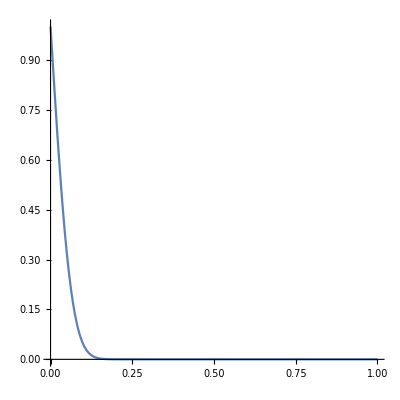
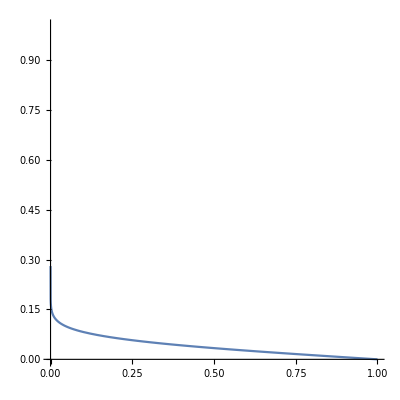
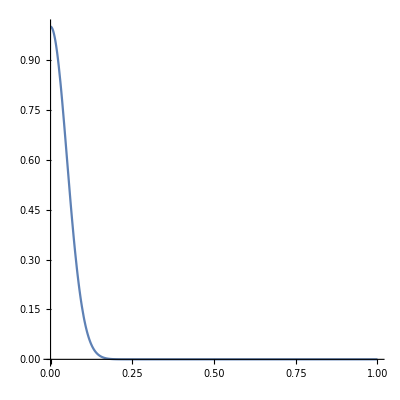
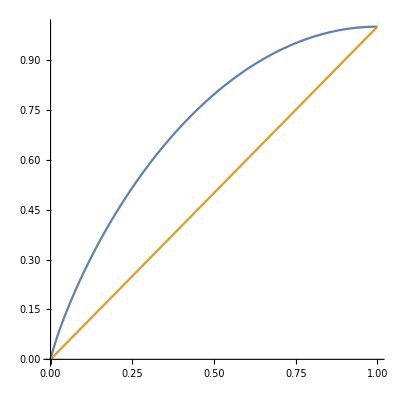

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

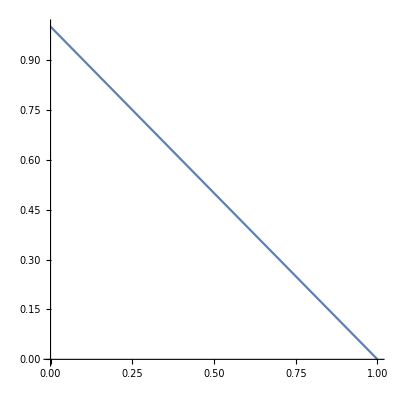
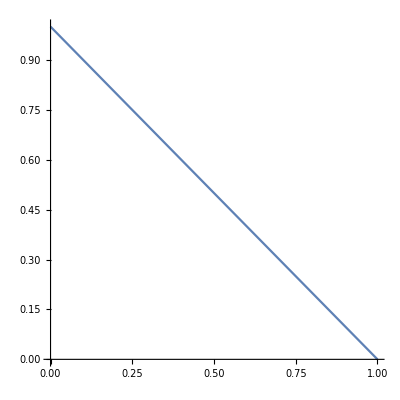
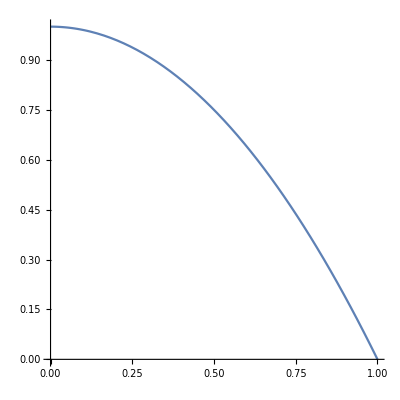
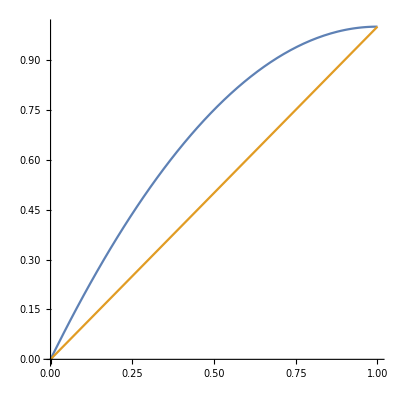

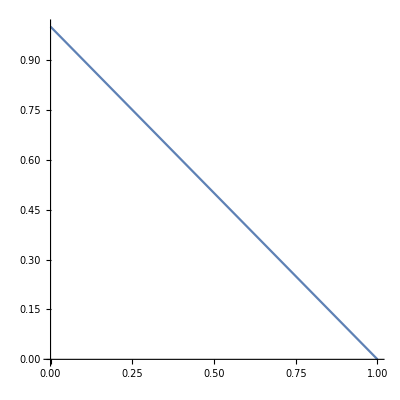
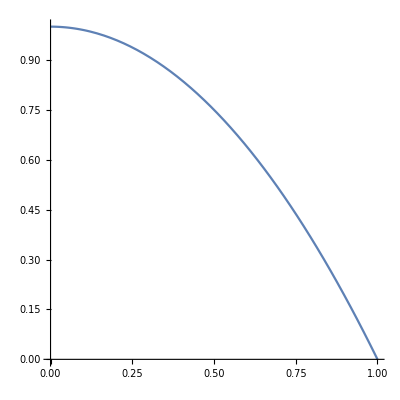
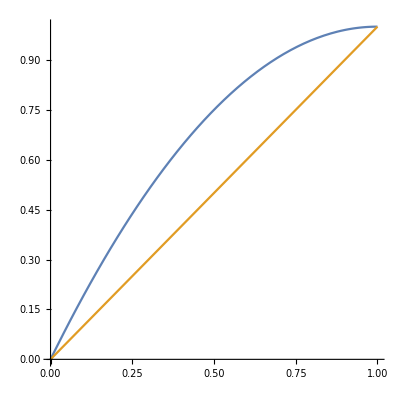
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

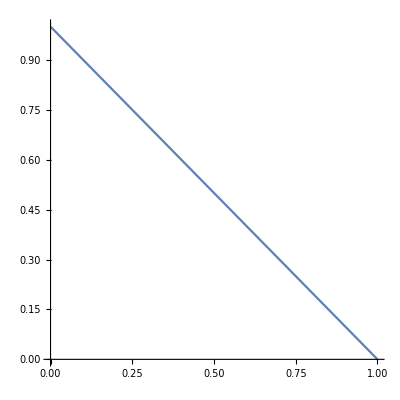
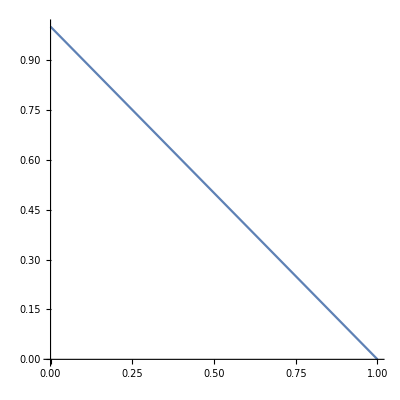
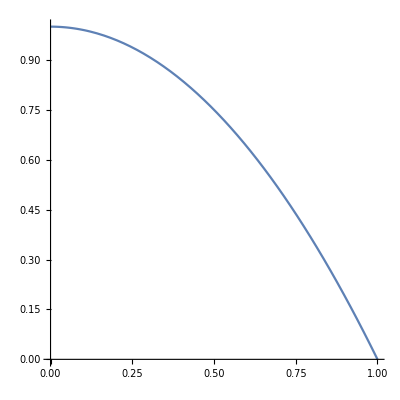
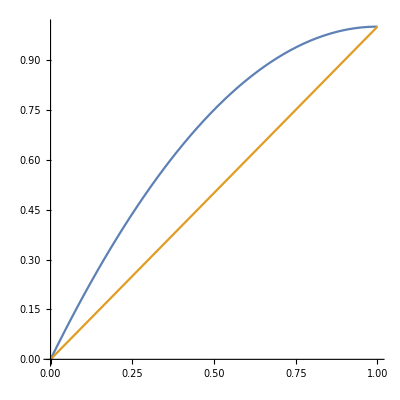

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

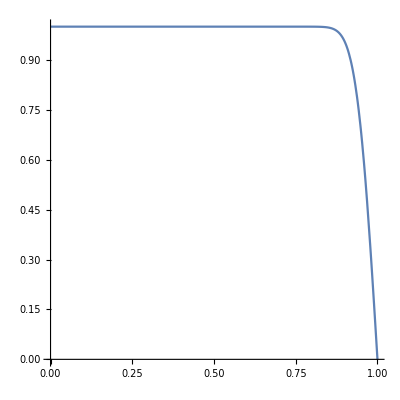
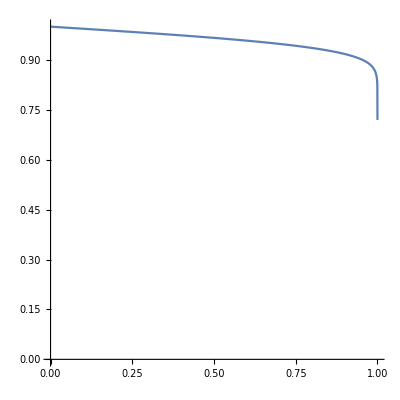
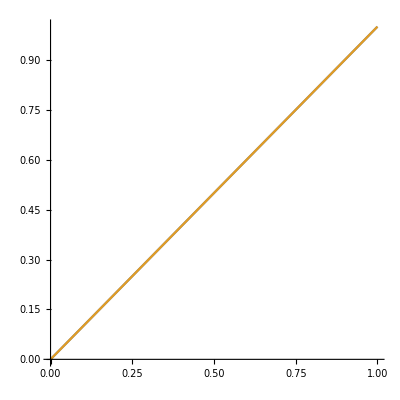
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TestROC[Exp[-x^2/(2 σ^2)]/(Sqrt[2π]σ)/.σ->0.05]
TestROC[Exp[-x^2/(2 σ^2)]/(Sqrt[2π]σ)/.σ->20]
TestROC[1]
TestROC[Exp[-(x-1)^2/(2 σ^2)]/(Sqrt[2π]σ)/.σ->20]
TestROC[Exp[-(x-1)^2/(2 σ^2)]/(Sqrt[2π]σ)/.σ->.05]
```

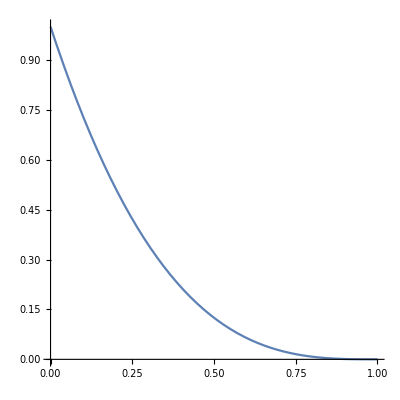
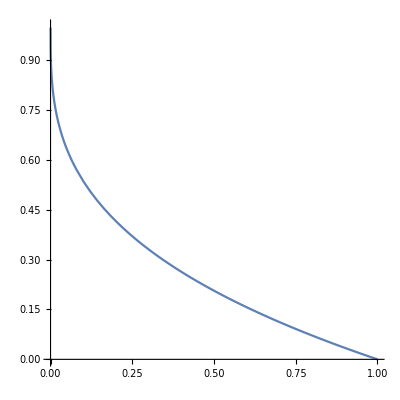
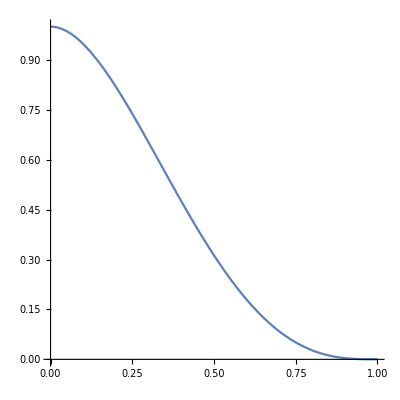
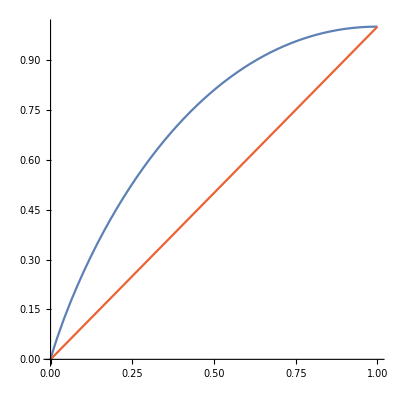

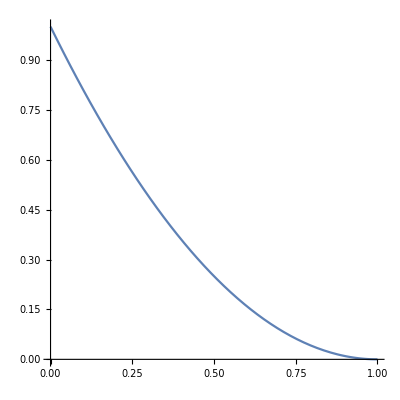
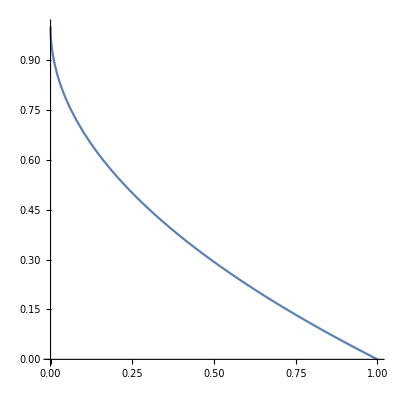
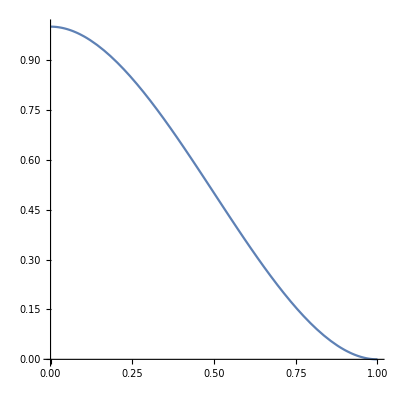
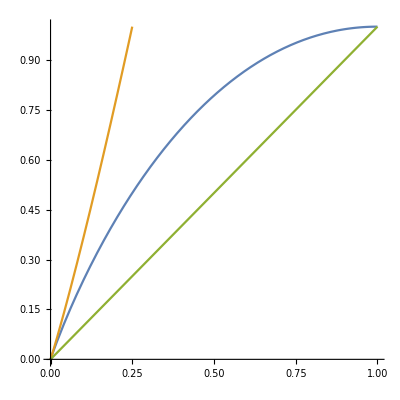

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

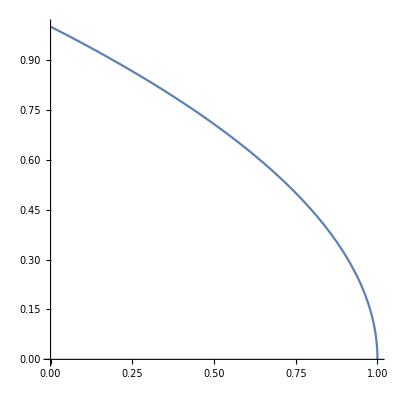
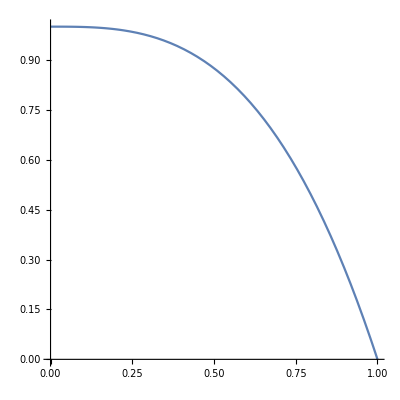
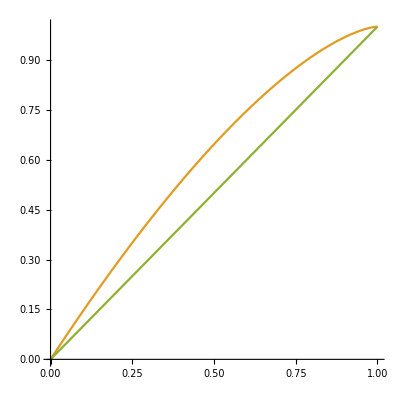
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

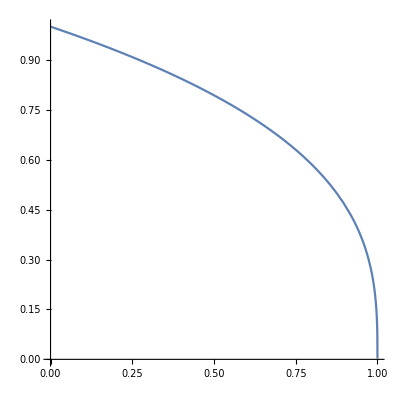
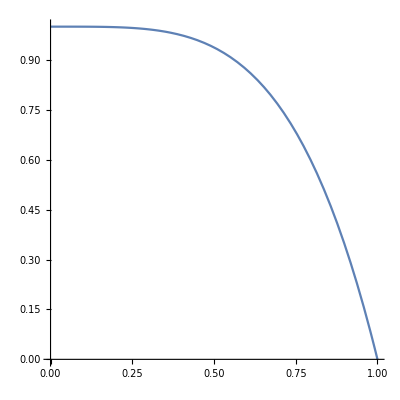
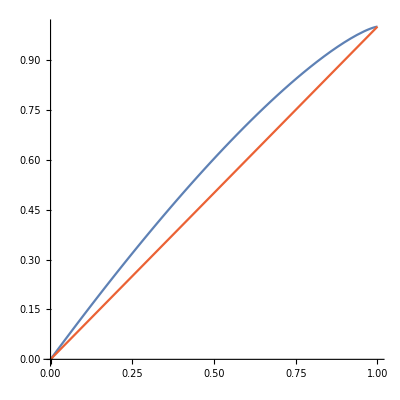
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TestROC[(1-x)^2]
TestROC[1-x]
TestROC[1]
TestROC[x]
TestROC[x^2]
```